# Live evaluation of expressions in TreeForm 3

## Introduction

This Mathematica notebook is licensed under a  
It is a demonstration that allows a user try values of input to solve an equation displayed in tree form, with the partial values shown at each stage of the calculation.  The idea behind the demonstration is discussed at length in .

The demonstration is a kludge that I made up to show what I was thinking of.   It should be possible to create a Mathematica command EvaluatableTreeForm that would produce a package showing a manipulatable tree form of any Mathematica expression.

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

## Construction

```mathematica
f[x_,y_]:=3x^2+2(1+y)
```

```mathematica
f[2,-3]
```

8

```mathematica
f[x,y]//TraditionalForm//TeXForm
```

3 x^2+2 (y+1)

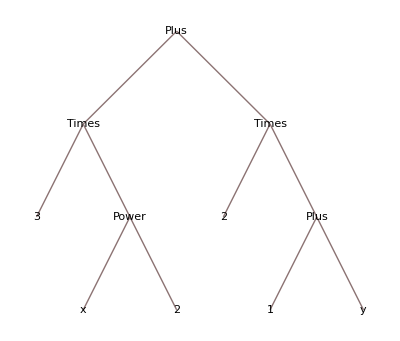

```mathematica
f[x,y]//TreeForm
```

```mathematica
tree1[step_,x_,y_]:=TreePlot[
{
{"Plus",1}->{"Times",2},
{"Plus",1}->{"Times",3},
{"Times",2}->{3,4},
{"Times",2}->{"Power",5},
{"Times",3}->{2,6},
{"Times",3}->{"Plus",7},
{"Power",5}->{x,8},
{"Power",5}->{2,9},
{"Plus",7}->{1,10},
{"Plus",7}->{y,11}},
EdgeRenderingFunction->(Style[Line[{#[[1]],#[[2]]}],Black]&),
VertexRenderingFunction->(Inset[Framed[Style[#2[[1]],14,Black,FontFamily->Arial],Background->White],#1]&),
VertexLabeling->True,ImageSize->250]
```

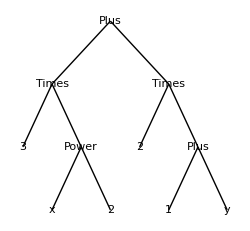

```mathematica
tree1[1,x,y]
```

```mathematica
vertexshow[step_]:=(Inset[Framed[Style[#2[[1]],14,Black,FontFamily->Arial],Background->White],#1]&)
```

```mathematica
edgeshow[step_]:=(Style[Line[{#[[1]],#[[2]]}],Black]&)
```

```mathematica
edgeshow [0]
```

Style[Line[{#1⟦1⟧,#1⟦2⟧}],Black]&

```mathematica
Style[3,Gray]
```

3

```mathematica
lighten[str_]:=Style[str,Gray]
```

```mathematica
lighten[3x]
```

3 x

```mathematica
tree2[step_,x_,y_]:=TreePlot[
{
{"Plus",1}->{"Times",2},
{"Plus",1}->{"Times",3},
{"Times",2}->{3,4},
{"Times",2}->{"Power",5},
{"Times",3}->{2,6},
{"Times",3}->{"Plus",7},
{"Power",5}->{x,8},
{"Power",5}->{2,9},
{"Plus",7}->{1,10},
{"Plus",7}->{y,11}},
EdgeRenderingFunction->edgeshow[step],
VertexRenderingFunction->vertexshow[step],
VertexLabeling->True,ImageSize->250]
```

```mathematica
tree2[0,x,y]
```

-Graphics-

```mathematica
Remove[x]
```

```mathematica
lab[s_,x_,y_,1]:=If[s≤5,"Plus",3x ^2+2(1+y)];lab[s_,x_,y_,2]:=If[s≤3,"Times",If[s≤5,3x ^2,lighten[3x^2]]];
lab[s_,x_,y_,3]:=If[s≤4,"Times",If[s≤5,2(1+y),lighten[1+y]]];lab[s_,x_,y_,4]:=If[s≤3,3,lighten[3]];
lab[s_,x_,y_,5]:=If[s<=1,"Power",If[s≤3,x ^2,lighten[x^2]]];
lab[s_,x_,y_,6]:=If[s≤4,2,lighten[2]];lab[s_,x_,y_,7]:=If[s≤2,"Plus",If[s≤4,1+y,lighten[1+y]]];lab[s_,x_,y_,8]:=If[s==0,"x",If[s==1,x,lighten[x]]];lab[s_,x_,y_,9]:=If[s≤1,"2",lighten[2]];lab[s_,x_,y_,10]:=If[s≤2,"1",lighten[1]];
lab[s_,x_,y_,11]:=If[s==0,"y",If[s≤2,y,lighten[y]]];
```

```mathematica
tree3[step_,x_,y_]:=TreePlot[
{
{lab[step,x,y,1],1}->{lab[step,x,y,2],2},
{lab[step,x,y,1],1}->{lab[step,x,y,3],3},
{lab[step,x,y,2],2}->{lab[step,x,y,4],4},
{lab[step,x,y,2],2}->{lab[step,x,y,5],5},
{lab[step,x,y,3],3}->{lab[step,x,y,6],6},
{lab[step,x,y,3],3}->{lab[step,x,y,7],7},
{lab[step,x,y,5],5}->{lab[step,x,y,8],8},
{lab[step,x,y,5],5}->{lab[step,x,y,9],9},
{lab[step,x,y,7],7}->{lab[step,x,y,10],10},
{lab[step,x,y,7],7}->{lab[step,x,y,11],11}
},
EdgeRenderingFunction->edgeshow[step],
VertexRenderingFunction->vertexshow[step],
VertexLabeling->True,ImageSize->250]
```

```mathematica
Manipulate[tree3[step,x,y],{{step,0},0,6,1},{{x,3.},-4.,4.},{{y,-2.},-4,4},SaveDefinitions->True]
```

```mathematica
tree[1,1,x,y]
```

tree[1,1,x,y]

```mathematica
Manipulate[tree[1,1,x,y],{{Step,1},{1,2,3}}]
```